# Лабораторная работа №2 Калиновский Владимир, ПО-4

## Задание 1

1.1 Придумайте и определите символьное выражение, содержащее не менее трех слагаемых, причем хотя бы одно из них должно быть рациональным выражением.

```mathematica
t1 = (6 x^3(y^2+11))/((4 x^3-3)(x+y))+(x+y)^2+x^3+y^3
Expand[t1]
```

x^3+y^3+(x+y)^2+(6 x^3 (11+y^2))/((-3+4 x^3) (x+y))

x^2+x^3+2 x y+y^2+y^3+(66 x^3)/((-3+4 x^3) (x+y))+(6 x^3 y^2)/((-3+4 x^3) (x+y))

```mathematica
ExpandAll[t1]
```

x^2+x^3+2 x y+y^2+y^3+(66 x^3)/(-3 x+4 x^4-3 y+4 x^3 y)+(6 x^3 y^2)/(-3 x+4 x^4-3 y+4 x^3 y)

```mathematica
Factor[t1] (*Выносит общий множитель за скобку*)
```

1/((-3+4 x^3) (x+y))(63 x^3-3 x^4+4 x^6+4 x^7-9 x^2 y-3 x^3 y+12 x^5 y+4 x^6 y-9 x y^2+6 x^3 y^2+12 x^4 y^2-3 y^3-3 x y^3+4 x^3 y^3+4 x^4 y^3-3 y^4+4 x^3 y^4)

```mathematica
Together[t1] (*Приведение к общему знаменателю, потом сокращает*)
```

1/((-3+4 x^3) (x+y))(63 x^3-3 x^4+4 x^6+4 x^7-9 x^2 y-3 x^3 y+12 x^5 y+4 x^6 y-9 x y^2+6 x^3 y^2+12 x^4 y^2-3 y^3-3 x y^3+4 x^3 y^3+4 x^4 y^3-3 y^4+4 x^3 y^4)

```mathematica
Apart [t1]
```

(x^2 (-3-3 x-6 x^2+4 x^3+4 x^4))/(-3+4 x^3)+(2 x (-3+3 x^2+4 x^3) y)/(-3+4 x^3)+y^2+y^3+(6 (11 x^3+x^5))/((-3+4 x^3) (x+y))

```mathematica
Cancel[t1]
```

```mathematica
x^3+y^3+(x+y)^2+(6 x^3 (11+y^2))/((-3+4 x^3) (x+y))
```

```mathematica
Simplify[t1] (*самая простая форма выражения*)
```

x^3+y^3+(x+y)^2+(6 x^3 (11+y^2))/((-3+4 x^3) (x+y))

1.2 Приведите выражение t1 к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения, обозначив его t2. С помощью функции Collect представьте выражение  t2 в виде полинома по степеням x или y. Определите максимальную степень n одной из переменных, например,  x, в выражении t2 и коэффициент при x^n Используйте функции Exponent и Сoefficient.

```mathematica
t2 = Numerator[Together[t1]];
t2
```

63 x^3-3 x^4+4 x^6+4 x^7-9 x^2 y-3 x^3 y+12 x^5 y+4 x^6 y-9 x y^2+6 x^3 y^2+12 x^4 y^2-3 y^3-3 x y^3+4 x^3 y^3+4 x^4 y^3-3 y^4+4 x^3 y^4

```mathematica
Collect[t2,y] (*Постройте полином*)
```

63 x^3-3 x^4+4 x^6+4 x^7+(-9 x^2-3 x^3+12 x^5+4 x^6) y+(-9 x+6 x^3+12 x^4) y^2+(-3-3 x+4 x^3+4 x^4) y^3+(-3+4 x^3) y^4

```mathematica
Exponent[t2,y]
```

4

```mathematica
Coefficient[t2,x,2]
```

-9 y

### Задание 2

1. Вычислить производную функции..

```mathematica
D[x^n Cos[x], x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

2. Вычислите производные..

```mathematica
D[(a*x^3+2 x^2),x]
```

4 x+3 a x^2

```mathematica
D[(4 x^2-5x+8-3/x),{x,3}] (*производная третьего порядка*)
```

18/x^4

```mathematica
D[(x^3 y^2+3 x^2),{x,3},{y,2}]
```

12

3. Используя функцию Integrate, вычислите интеграл.

```mathematica
Integrate[ 1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

4. Вычислите интегралы, затем продифферинцируйте полученные выражения и убедитесь в том, что получаемые результаты совпадают с подынтегральными выражениями.

```mathematica
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Together[D[x^2/2-1/2 Log[1+x^2],x]]
```

x^3/(1+x^2)

```mathematica
Simplify[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]]
```

1/(1+x^3)

5. Вычислите определенный интеграл

```mathematica
Integrate[5x-2 √x+ 32/x^3,{x,1,4}]
```

259/6

6. Вычислите интегралы.

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1.}]
```

1.05753

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1}]
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

### Задание 3

1. Используя функцию Solve, решить уравнение.

```mathematica
Solve[ax^4+x^2+3==0,x]
```

{{x→-√(-3-ax^4)},{x→√(-3-ax^4)}}

2. Найти точное решение системы уравнений.

```mathematica
Solve[x^2+y==1 && y^2-x^2==2, {x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

3. Решить систему уравнений:

```mathematica
NSolve[x^2-y^2==1&& y^3+x==5, {x,y}]
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

4. Найдите общие решения дифференциальных уравнений, используя DSolve. Найти графики.

```mathematica
equation1 =y'[x]-y[x]Tan[x]==x
```

-Tan[x] y[x]+y'[x]==x

```mathematica
equation2 =y'[x]+y[x]Tan[x]==1/Cos[x]
```

Tan[x] y[x]+y'[x]==Sec[x]

```mathematica
generalsolution1 = DSolve[equation1, y[x],{x}]
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
generalsolution2 = DSolve[equation2, y[x],x]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

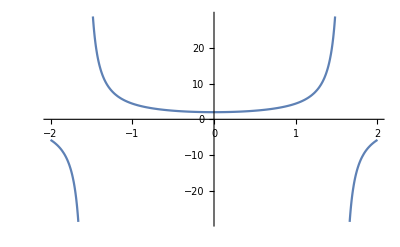

```mathematica
Plot[Evaluate[y[x]/. generalsolution1 /. {C[1] ->1}],{x,-2,2}] (*/. - ReplaceAll*)
(* Plot[Evaluate[C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x]) ./ {C[1] ->1}],{x,-2,2}] *)
```

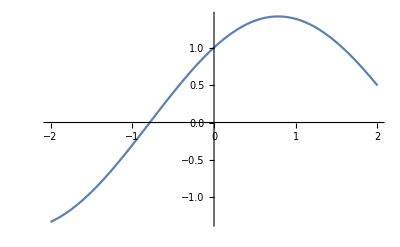

```mathematica
Plot[Evaluate[y[x]/. generalsolution2 /. {C[1] ->1}],{x,-2,2}]
```

5. Самостоятельно выбрав граничные условия, найдите решение дифференциального уравнения в символьном виде. С помощью NDSolve найдите решение в численном виде. На одной координатной плоскости отобразите обе функции и покажите, что они совпадают.

```mathematica
equation3 = DSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x], x]
```

{{y[x]→(ⅇ^(x/2) (-(-1)^(2/3) AiryAi[-(-1)^(1/3) (1/4-x)] AiryBi[-1/4 (-1)^(1/3)]+(-1)^(2/3) AiryAi[-1/4 (-1)^(1/3)] AiryBi[-(-1)^(1/3) (1/4-x)]+2 AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-(-1)^(1/3) (1/4-x)]-2 AiryAi[-(-1)^(1/3) (1/4-x)] AiryBiPrime[-1/4 (-1)^(1/3)]))/(2 (AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-1/4 (-1)^(1/3)]-AiryAi[-1/4 (-1)^(1/3)] AiryBiPrime[-1/4 (-1)^(1/3)]))}}

```mathematica
equation4 = NDSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1},y[x],{x, -2, 2}]
```

{{y[x]→InterpolatingFunction[…][x]}}

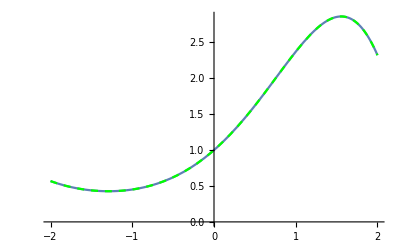

```mathematica
(* 
Pick out a part of a matrix:
In[1]:={{a,b,c},{d,e,f},{g,h,i}}[[2,3]] 
   Out[1]= f 
*)
Show[
Plot[equation3[[1,1,2]],{x,-2,2}], Plot[equation4[[1, 1, 2]], {x, -2, 2},PlotStyle->{Dashed, Green}]]
```